```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Data = Import["../telefile.txt","Table"];
nx = Data[[1,2]];
hx = Data[[1,4]];
tau = Data[[1,6]];
deltacnt=Data[[1,8]];
nshape = Data[[1,10]]
xcnt = Data[[2]];
nsteps=Length[Data]-2
His = Data[[3;;]];
PlotDGfile[q_,t_,diap_]:=Module[{H,sl,sr,otr},
H=Partition[His[[t]],(Dimensions[His][[2]])/nx];
sl=Sum[(-1)^(nshape-1-s)H[[All,nshape q-s]],{s,0,nshape-1}];
sr=Sum[H[[All,nshape q-s]],{s,0,nshape-1}];
(*Print[ToString[sl]<>" "<>ToString[sr]];*)
otr=Table[{{xcnt[[i]]-hx/2,sl[[i]]},{xcnt[[i]]+hx/2,sr[[i]]}},{i,1,nx}];
ListLinePlot[otr,PlotRange->{diap[[1]],diap[[2]]},PlotStyle->Directive[{Thick}],AxesStyle->{{Directive[16],Thick},{Directive[16],Thick}},AxesOrigin->{0,-0.1}]];
(*Восстановленное решение - кусочно-линейное*)
numsollin[q_,x_,t_]:=Module[{H,u,v,w,cell,sl,sr,otr},
H=Partition[His[[t]],(Dimensions[His][[2]])/nx];
u=H[[All,nshape(q-1)+1]];
v=H[[All,nshape(q-1)+2]];
If[nshape==3,w=H[[All,nshape(q-1)+nshape]],w=0 H[[All,nshape(q-1)+nshape]]];
cell=Floor[x/hx]+1;
u[[cell]]+(x-hx(cell-1/2))/(hx/2)v[[cell]]+0((x-hx(cell-1/2))^2/(hx^2/6)-1/2)w[[cell]]
];
numsol[q_,x_,t_]:=Module[{H,u,v,w,cell,sl,sr,otr},
H=Partition[His[[t]],(Dimensions[His][[2]])/nx];
u=H[[All,nshape(q-1)+1]];
v=H[[All,nshape(q-1)+2]];
If[nshape==3,w=H[[All,nshape(q-1)+nshape]],w=0H[[All,nshape(q-1)+nshape]]];
cell=Floor[x/hx]+1;
u[[cell]]+(x-hx(cell-1/2))/(hx/2)v[[cell]]+((x-hx(cell-1/2))^2/(hx^2/6)-1/2)w[[cell]]
];
```

2

201

```mathematica
numsolListPlot[q_,t_]:=Module[{H,u,v,w,cell,sl,sr,otr,i},
H=Partition[His[[t]],(Dimensions[His][[2]])/nx];
u=H[[All,nshape(q-1)+1]];
(*v=H[[All,nshape(q-1)+2]];
If[nshape==3,w=H[[All,nshape(q-1)+nshape]],w=0 H[[All,nshape(q-1)+nshape]]];*)
ListPlot[Table[{hx(i-1/2),u[[i]]},{i,1,Length[u]}], PlotRange->All]
(*cell=Floor[x/hx]+1;
u[[cell]]+(x-hx(cell-1/2))/(hx/2)v[[cell]]+((x-hx(cell-1/2))^2/(hx^2/6)-1/2)w[[cell]]*)
];
```

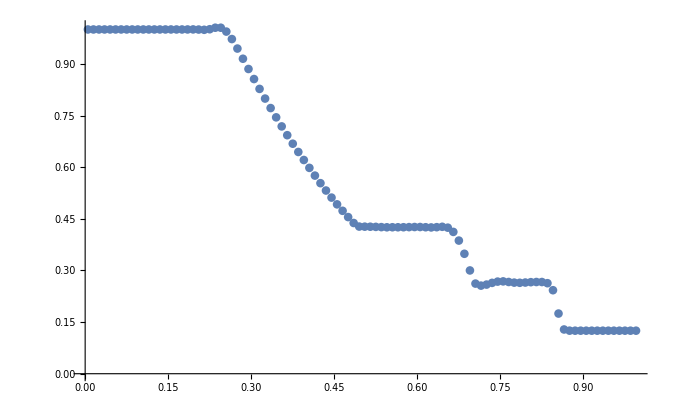

```mathematica
numsolListPlot[1,nsteps]
```

```mathematica
Manipulate[Plot[numsol[1,x,t],{x,0,1},PlotRange->All,PlotPoints->100],{t,1,nsteps,1}]
```

```mathematica
Manipulate[PlotDGfile[1,t,{-0.2,1.2}],{t,1,nsteps,1}]
```

```mathematica
Partition[Partition[His[[2]],13][[50]],2]
```

{{0.953682,-0.105362},{0.0474588,0.10537},{0,0},{0,0},{2.36784,-0.279179},{2.36666,0}}

```mathematica
Manipulate[PlotDGfile[2,t,{-0.1,0.5}],{t,1,nsteps,1}]
```

```mathematica
Manipulate[PlotDGfile[5,t,{0,3.0}],{t,1,nsteps,1}]
```

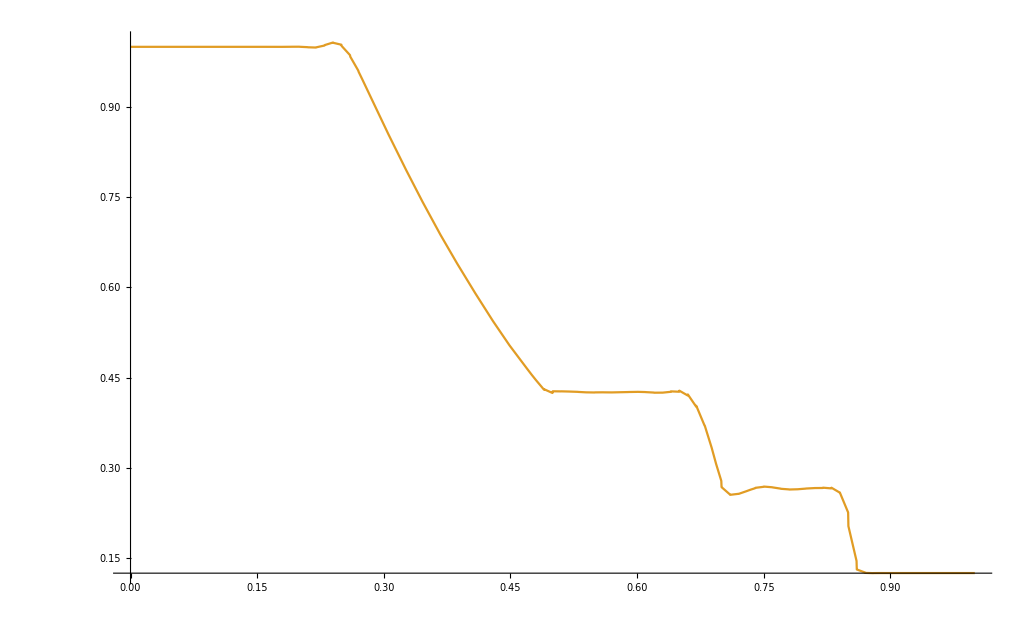

```mathematica
Plot[{ρ[x,0.2],numsol[1,x,nsteps]},{x,0,1},Exclusions->None,PlotRange->All]
```

```mathematica
200 with weights 0.001
```

0.2 weights with

```mathematica
200 with weights 0.01
```

2. weights with

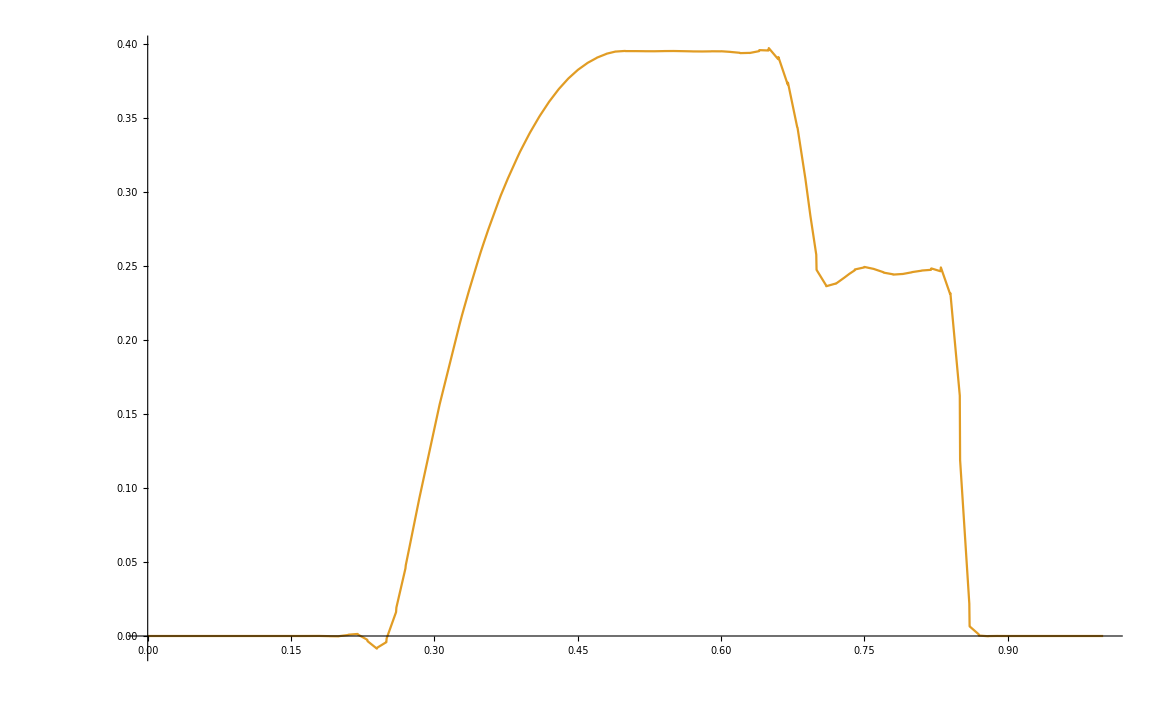

```mathematica
Plot[{ρu[x,0.2],numsol[2,x,nsteps]},{x,0,1},Exclusions->None,PlotRange->All]
```

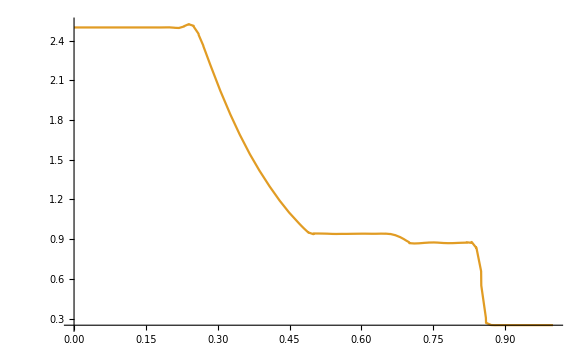

```mathematica
Plot[{e[x,0.2],numsol[5,x,nsteps]},{x,0,1},Exclusions->None,PlotRange->All]
```

```mathematica
$MaxPiecewiseCases=nx+2;
```

```mathematica
(*Вычисление нормы C*)
```

```mathematica
(*Вычисление нормы L1*)
```